```mathematica
ClearAll["`*"]
$HistoryLength=5;
RunScheduledTask[NotebookSave[EvaluationNotebook[]],5000];
```

## System Definition

```mathematica
nAA=20;(*Number of amino-acid species*)
tmax=10000.;(*Maximal time for dynamic simulation*)
cellVolume=2.5*10^-15(*Cell volume*);
nAvogadro=6*10^23(*Avagado number*);
proteinContent=15*10^8(*aa/Cell: Bremer Dennis 1996*);
```

### Chemical species and parameters in the model

Chemical species related to aa-synthesis

```mathematica
csI={
aa,(*amino-acids*)
taa,(*charged tRNA*)
tf,(*uncharged tRNA*)
e,(*Enzyme catalyzing amino-acid synthesis*)
sTot,(*Enzyme catalyzing aa-tRNA synthase*)
rtf,(*Ribosome with uncharged tRNA in A-site*)
rf (*Ribosome with "free" A-site*)
};
```

Rate equations related to aa-synthesis

```mathematica
vI={
vAAsynt,(*Amino-acid synthesis*)
vtRNAchar(*rate of aa-tRNA synthase*)
};
```

Parameters related to amino-acid synthesis

```mathematica
parI={
(*vAAsynth*)
kn,(*kcat of amino-acid synthesis*)
kIa, (*kI of amino-acids for am*)
(*vtRNAchar*)
ks,(*kcat of aa-tRNA synthase*)
kMaa,(*kM of amino acids*)
kMtf(*kM of uncharged tRNA*),
(*other*)
f(*Fraction of amino-acid in biomass composition*),
τ(*Ratio tRNAi/ribosome*)
};
```

```mathematica
(*Function to appand index to variables and parameters
Input: index number*)
appendI[i_]:=#->ToExpression[ToString[#]<>ToString[i]]&/@Join[csI,vI,parI]
(*Append index for all AA species *)
appendAllI:=appendI[#]&/@Range[nAA]
```

Independent variables

```mathematica
(*amino acids*)
aaSpecies=aa/.appendI[#]&/@Range[nAA];
(*Charged tRNAs: taa*)
taaSpecies=taa/.appendI[#]&/@Range[nAA];
```

```mathematica
varsNoRegulation=Join[
aaSpecies,
taaSpecies
];
varsQSS=Join[
varsNoRegulation,
{ppGpp}
];
vars=Join[
varsNoRegulation,
{r,ppGpp}
];
```

Dependent variables (uncharged tRNAs)

```mathematica
(*Free/uncharged tRNAs: tf*)
tfSpecies =tf/.appendI[#]&/@Range[nAA];
depVars=tfSpecies;
```

```mathematica
tTot=Total[r*τ/.appendAllI];
```

```mathematica
rtfSpecies=rtf/.appendAllI;
```

```mathematica
rfSpecies=rf/.appendAllI;
```

### Rate equations

#### Amino-acids metabolism and protein synthesis

Rate equations of amino acid synthesis:
vi = kmi * ei * (1-r) *1/(1+ai/ki),

```mathematica
ratesAAsynt=(vAAsynt-> kn e bm/nAmet(1-r[t]/rmax)1/(1+aa[t]/kIa))/.appendAllI;
```

Rate equations for tRNA charging:

```mathematica
ratestRNAchar=vtRNAchar-> ks*sTot*(tf/kMtf*aa[t]/kMaa)/(aa[t]/kMaa+tf/kMtf+aa[t]/kMaa tf/kMtf)/.appendAllI;
```

#### Polypetide and ribosome synthesis

Rate of polypetide synthesis

```mathematica
numeratorRibosome=Simplify[1+Total[f*(κrta/taa[t]+tf/taa[t]*κrta/κrt)/.appendAllI]];
```

```mathematica
vR= (krib*r[t])/numeratorRibosome;
μ=(*conversion from per s to per hour*)(vR(*M amino acids/s*))/(bm(*M amino acids*));
```

```mathematica
drate=3600(μ/.x_[t]->x)/Log[2];(*Conver specific growth rate to doubling rate*)
```

```mathematica
vrrnInit=vInitMax*rnapF/(kMrrn+rnapF)*1/(1+(ppGpp[t]/kIppGpp)^nppGpp)*(1(*convert Nrib to Molar*))/(cellVolume*nAvogadro/10^6); (*rate of rrn transcription initiation*)
```

```mathematica
ratesGrowth={
vribosome->vR(*in aa/s*),
vRsynt->Min[vrrnInit,γmax vR/nARib],(*Rate of ribosome synthesis*)
vRdilution->r[t]*μ(*Dilution rate per second*)
};
```

```mathematica
rtfSolutions=rtf-> r[t]*(f*tf/taa[t] κrta/κrt)/numeratorRibosome/.appendAllI;(*Calculate concentration of each uncharged tRNA*)
```

```mathematica
rfSolution=rf-> (f*κrta/taa[t])/numeratorRibosome/.appendAllI;
```

```mathematica
rtfTot=Simplify[Total[rtfSpecies/.rtfSolutions]];(*Sum of all concentration of uncharged tRNA*)
```

```mathematica
ratesppGpp={
vRelA-> kRelA*RelAtot*1/(1+kDRelA/rtfTot),(*[RelA] saturating*)
vSpoTdeg->kSpoTdeg*ppGpp[t]};
```

```mathematica
ClearAll[rates]
rates=Join[
ratestRNAchar,
ratesAAsynt,
ratesGrowth,
ratesppGpp
];
```

### Odes

ODEs for amino acid species:
ai’ = vAAsynti - vtRNAchari

```mathematica
odesAA=(aa'[t]==vAAsynt-vtRNAchar)/.appendAllI;
```

ODEs for tRNA charging
tRNAaa’ = vtRNAchari - fi vribosome

```mathematica
odesTAA=taa'[t]==vtRNAchar-f*vribosome/.appendAllI;
```

ODEs for ppGpp metabolism

```mathematica
ClearAll[odesNoRegulation]
odesNoRegulation=Join[
odesAA,odesTAA
];
```

```mathematica
odesppGpp={ppGpp'[t]==vRelA +vSpoTSynt - vSpoTdeg };
```

ODEs for macromolecular composition

```mathematica
odesMacromolComp={r'[t] == vRsynt - vRdilution};
```

```mathematica
odesQSS=Join[odesNoRegulation,odesppGpp];
```

```mathematica
odes=Join[
odesNoRegulation,
odesppGpp,
odesMacromolComp];
```

### Relations between dependent variables

Total amount of each tRNA species. Neglect fraction the is bound to ribosome. This fraction is small and also relatively constant (if κrta=κrt, it is constant)

```mathematica
tmpRelations=Solve[
τ*r[t]==tf+taa[t]/.appendI[#]&/@Range[nAA],
tfSpecies];
tmpRelations//Length
relations=Flatten[tmpRelations];
Clear[tmpRelations]
```

1

### Parameters

```mathematica
pars={(*Amino-acid synthesis*)
e-> .05,
kn->.5,
kIa->10^2,
(*tRNA-aa synthese*)
sTot->1,
ks->100,
kMaa->100,(*ksi/kai in Elf and Ehrenberg, 2005*)
kMtf->1,(*KSi in Elf and Eherenberg, 2005*)

(*protein elongation*)
krib->20,
κrta->1,
κrt->500,

(*ppGpp synthesis*)
kRelA->(*4500./60*)75,(*cf. Jenvert , Schiavone, FEBS Journal 2005*)
RelAtot->(100(*100 per cell*))/(nAvogadro*cellVolume/10^6),
kDRelA->2.6*10^-1,
vSpoTSynt->.001,
kSpoTdeg->Log[2.]/30,(*Half life time of 120s: Literature value suggests 120-150s, but this gives rise to ppGpp levels not consistent with Subscript[k, IppGpp]*)

(*Ribosome synthesis*)
vInitMax-> 2000,(*Estimatied from Klumpp, Hwa *)
rnapF->1.(*Klumpp, Hwa 2008*),
kMrrn->20(*Klumpp, Hwa 2008*),
kIppGpp->1.(*1 μM, Paul et al, 2004*),
nppGpp->1.,
γmax->1.(*Maximal fraction of ribosome capacity dedicated to ribosome synthesis*),
(*other*)
τ->.5,(*tRNAi/r*)
f->1/20.,
bm->proteinContent/(cellVolume*nAvogadro/10^6)(*Biomass concentration in Molar amino-acids*),
nARib->7459(*aa/ribosome: BNID 101175*)*1.65(*Ratio "extended ribosome"/ribosome*),
nAmet-> 300(*Avarage size of a protein*),
rmax-> proteinContent/(cellVolume*nAvogadro/10^6)/(7459*1.65)(*ribosomal concentratation when all biomass is ribosome. Equivalent to [total protein] and p*)
}/.appendAllI//Flatten//DeleteDuplicates;
SeedRandom[0]
pars=pars/.(Rule[#->_,#->fac*RandomVariate[LogNormalDistribution[Log[1.],.2]]]&/@(kn/.appendAllI));
pars=pars/.fac->0.2
```

{e1→0.05,kn1→0.176694,kIa1→100,sTot1→1,ks1→100,kMaa1→100,kMtf1→1,krib→20,κrta→1,κrt→500,kRelA→75,RelAtot→0.0666667,kDRelA→0.26,vSpoTSynt→0.001,kSpoTdeg→0.0231049,vInitMax→2000,rnapF→1.,kMrrn→20,kIppGpp→1.,nppGpp→1.,γmax→1.,τ1→0.5,f1→0.05,bm→1.×10^6,nARib→12307.3,nAmet→300,rmax→81.2523,e2→0.05,kn2→0.170472,kIa2→100,sTot2→1,ks2→100,kMaa2→100,kMtf2→1,τ2→0.5,f2→0.05,e3→0.05,kn3→0.215015,kIa3→100,sTot3→1,ks3→100,kMaa3→100,kMtf3→1,τ3→0.5,f3→0.05,e4→0.05,kn4→0.16053,kIa4→100,sTot4→1,ks4→100,kMaa4→100,kMtf4→1,τ4→0.5,f4→0.05,e5→0.05,kn5→0.154008,kIa5→100,sTot5→1,ks5→100,kMaa5→100,kMtf5→1,τ5→0.5,f5→0.05,e6→0.05,kn6→0.232252,kIa6→100,sTot6→1,ks6→100,kMaa6→100,kMtf6→1,τ6→0.5,f6→0.05,e7→0.05,kn7→0.188972,kIa7→100,sTot7→1,ks7→100,kMaa7→100,kMtf7→1,τ7→0.5,f7→0.05,e8→0.05,kn8→0.202409,kIa8→100,sTot8→1,ks8→100,kMaa8→100,kMtf8→1,τ8→0.5,f8→0.05,e9→0.05,kn9→0.221447,kIa9→100,sTot9→1,ks9→100,kMaa9→100,kMtf9→1,τ9→0.5,f9→0.05,e10→0.05,kn10→0.175156,kIa10→100,sTot10→1,ks10→100,kMaa10→100,kMtf10→1,τ10→0.5,f10→0.05,e11→0.05,kn11→0.218931,kIa11→100,sTot11→1,ks11→100,kMaa11→100,kMtf11→1,τ11→0.5,f11→0.05,e12→0.05,kn12→0.18925,kIa12→100,sTot12→1,ks12→100,kMaa12→100,kMtf12→1,τ12→0.5,f12→0.05,e13→0.05,kn13→0.182501,kIa13→100,sTot13→1,ks13→100,kMaa13→100,kMtf13→1,τ13→0.5,f13→0.05,e14→0.05,kn14→0.168797,kIa14→100,sTot14→1,ks14→100,kMaa14→100,kMtf14→1,τ14→0.5,f14→0.05,e15→0.05,kn15→0.178173,kIa15→100,sTot15→1,ks15→100,kMaa15→100,kMtf15→1,τ15→0.5,f15→0.05,e16→0.05,kn16→0.163557,kIa16→100,sTot16→1,ks16→100,kMaa16→100,kMtf16→1,τ16→0.5,f16→0.05,e17→0.05,kn17→0.240562,kIa17→100,sTot17→1,ks17→100,kMaa17→100,kMtf17→1,τ17→0.5,f17→0.05,e18→0.05,kn18→0.234708,kIa18→100,sTot18→1,ks18→100,kMaa18→100,kMtf18→1,τ18→0.5,f18→0.05,e19→0.05,kn19→0.238857,kIa19→100,sTot19→1,ks19→100,kMaa19→100,kMtf19→1,τ19→0.5,f19→0.05,e20→0.05,kn20→0.192553,kIa20→100,sTot20→1,ks20→100,kMaa20→100,kMtf20→1,τ20→0.5,f20→0.05}

### Initial conditions

```mathematica
ClearAll[init]
```

```mathematica
initAA=aa[0]==1/.appendAllI;
initTAA=(taa[0]==.6*τ*r[0])/.appendAllI;
initNoRegulation=Join[
initAA,
initTAA/.r[0]->r
];
initQSS=Join[
initNoRegulation/.r[0]->r,
{ppGpp[0]==1}
];
```

```mathematica
ClearAll[init]
init=Flatten[{
r[0]==.2*rmax/.pars,
ppGpp[0]==kIppGpp/.pars,
aa[0]==kIa/.appendAllI/.pars,
taa[0]==.1*τ*rmax/.appendAllI/.pars
}];
```

## System analysis

### Model without regulation (but with ppGpp metabolism)

```mathematica
sysQSS=odesQSS/.rates/.relations/.r[t]->r;
```

```mathematica
ClearAll[soltQSS]
(*Use this function to simulate temportal dynamics*)
soltQSS[rval_,PARS_]:=
NDSolve[
(Join[sysQSS,initQSS]/.PARS/.r->rval),
varsQSS,
{t,0,tmax}
 ]//Flatten

(*Usage*)
rinput = 0.3*rmax/.pars
sol = soltQSS[rinput,pars];
Plot[
Evaluate[{ppGpp[t],aa1[t],aa2[t],aa5[t],taa1[t],taa2[t],taa5[t]}/.sol],
{t,0,500},
AxesLabel->{"time","concentration"},
PlotLegends->{"ppGpp", "a_1", "a_2","a_5","t_a1","t_a2","t_a5"}
]
```

24.3757

Plot::optx: Unknown option PlotLegends in Plot[« 1 »].

Plot[{InterpolatingFunction[{{0.,10000.}},<>][t],InterpolatingFunction[{{0.,10000.}},<>][t],InterpolatingFunction[{{0.,10000.}},<>][t],InterpolatingFunction[{{0.,10000.}},<>][t],InterpolatingFunction[{{0.,10000.}},<>][t],InterpolatingFunction[{{0.,10000.}},<>][t],InterpolatingFunction[{{0.,10000.}},<>][t]},{t,0,500},AxesLabel→{time,concentration},PlotLegends→{ppGpp,a_1,a_2,a_5,t_a1,t_a2,t_a5}]

```mathematica
ClearAll[ssQSS]
(*Use this function to calculate the steady state.
It uses a time simulation to first approximate the steady state, which is used as imput to a rootfinding function*)
ssQSS[rval_?NumericQ,P_]:=Block[{tsol,ssguess,aaguess,taaguess,sol,ppGppguess,PARS},
PARS=Append[Cases[P,Except[r->_]],r->rval];
tsol=NDSolve[
Join[sysQSS,initQSS]/.PARS,
varsQSS,
{t,0,tmax}];
aaguess=Flatten[{#,#[tmax]/.tsol,$MachineEpsilon,∞}]&/@aaSpecies;
taaguess=Flatten[{#,
Max[2*$MachineEpsilon,Min[#[tmax]/.tsol,.99*τ1*r/.PARS]],
$MachineEpsilon,
τ1*r/.PARS}]&/@taaSpecies;
ppGppguess=Flatten[{ppGpp,ppGpp[tmax]/.tsol,$MachineEpsilon,∞}];
sol=FindRoot[
Thread[0==sysQSS⟦All,2⟧]/.x_[t]->x/.PARS,
Join[aaguess,taaguess,{ppGppguess}]
];
(*Print[r/.PARS];*)
Flatten[{
sol/.x_[t]->x,
relations/.x_[t]->x/.sol/.PARS,
jR->(vR/.relations/.x_[t]->x/.sol/.PARS)}
]
];

(*Calculate growth rate as function of ribosomal content*)
rinput = 0.3*rmax/.pars
sol = scanQSS=Table[
Append[ssQSS[rval,pars],r->rval],
{rval,.05*rmax/.pars,.45*rmax/.pars,.025*rmax/.pars}
]//Quiet;
```

24.3757

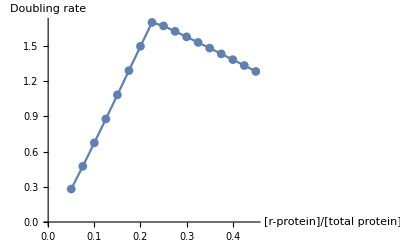

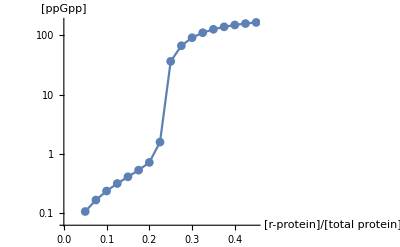

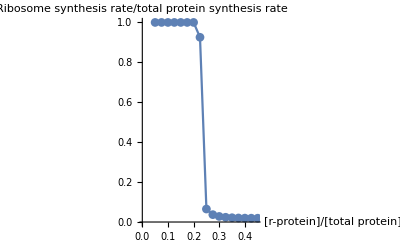

```mathematica
ListPlot[{r/rmax,drate}/.pars/.sol,
Joined->True,
PlotMarkers->Automatic,
AxesLabel->{"[r-protein]/[total protein]","Doubling rate"}]


ListLogPlot[{r/rmax, ppGpp}/.pars/.sol,
Joined->True,
PlotMarkers->Automatic,
AxesLabel->{"[r-protein]/[total protein]","[ppGpp]"}
]


ListPlot[{r/rmax,(vRsynt*nARib)/vribosome}/.rates/.relations/.x_[t]->x/.pars/.sol,
Joined->True,
PlotMarkers->Automatic,
AxesLabel->{"[r-protein]/[total protein]","Ribosome synthesis rate/total protein synthesis rate"}
]

(*ssQSS[rinput,pars]//TableForm*)
```

```mathematica
vribosome/.rates/.x_[t]->x/.ssQSS[0.3*rmax/.pars,pars]/.r->0.3*rmax/.pars
```

304.029

```mathematica
ClearAll[optimum]
(*Use this function to calculate the optimum
It searches for the ribosomal content r that maximises the biomass synthesis flux jR
*)
optimum[P_]:=Block[{mu,opt,rcrit,minAAsyn,PARS},
PARS=Cases[P,Except[r->_]];
minAAsyn=Min[(kn*e)/f nARib/nAmet/.appendAllI/.PARS];
rcrit=minAAsyn/(krib+minAAsyn)*rmax/.PARS;
mu[rval_?NumericQ]:=jR/.ssQSS[rval,PARS];
opt:=FindMaximum[mu[rval],{rval,.8*rcrit,1.2*rcrit,$MachineEpsilon,rmax/.PARS}];
{r->(rval/.opt⟦2⟧),ssQSS[(rval/.opt⟦2⟧),PARS],PARS}//Flatten
]//Quiet
(*Usage (NB: this may take a while)*)
opt=optimum[pars];
opt//TableForm
```

r→18.4814
aa1→38.1426
aa2→33.2784
aa3→68.1025
aa4→25.505
aa5→20.406
aa6→81.5788
aa7→47.7414
aa8→58.247
aa9→73.1314
aa10→36.94
aa11→71.164
aa12→47.9594
aa13→42.6826
aa14→31.9686
aa15→39.2987
aa16→27.8721
aa17→88.0758
aa18→83.4992
aa19→86.7429
aa20→50.541
taa1→8.83259
taa2→8.75693
taa3→8.96321
taa4→8.37207
taa5→3.41066
taa6→8.98071
taa7→8.90484
taa8→8.94266
taa9→8.97077
taa10→8.81786
taa11→8.96799
taa12→8.90591
taa13→8.87429
taa14→8.72629
taa15→8.84504
taa16→8.56695
taa17→8.98668
taa18→8.9826
taa19→8.98555
taa20→8.91744
ppGpp→3.46565
tf1→0.408115
tf2→0.483774
tf3→0.277496
tf4→0.868629
tf5→5.83004
tf6→0.259995
tf7→0.335862
tf8→0.298044
tf9→0.269932
tf10→0.422843
tf11→0.272715
tf12→0.334791
tf13→0.366413
tf14→0.514412
tf15→0.395661
tf16→0.673754
tf17→0.254023
tf18→0.258103
tf19→0.255154
tf20→0.323264
jR→329.379
e1→0.05
kn1→0.176694
kIa1→100
sTot1→1
ks1→100
kMaa1→100
kMtf1→1
krib→20
κrta→1
κrt→500
kRelA→75
RelAtot→0.0666667
kDRelA→0.26
vSpoTSynt→0.001
kSpoTdeg→0.0231049
vInitMax→2000
rnapF→1.
kMrrn→20
kIppGpp→1.
nppGpp→1.
γmax→1.
τ1→0.5
f1→0.05
bm→1.×10^6
nARib→12307.3
nAmet→300
rmax→81.2523
e2→0.05
kn2→0.170472
kIa2→100
sTot2→1
ks2→100
kMaa2→100
kMtf2→1
τ2→0.5
f2→0.05
e3→0.05
kn3→0.215015
kIa3→100
sTot3→1
ks3→100
kMaa3→100
kMtf3→1
τ3→0.5
f3→0.05
e4→0.05
kn4→0.16053
kIa4→100
sTot4→1
ks4→100
kMaa4→100
kMtf4→1
τ4→0.5
f4→0.05
e5→0.05
kn5→0.154008
kIa5→100
sTot5→1
ks5→100
kMaa5→100
kMtf5→1
τ5→0.5
f5→0.05
e6→0.05
kn6→0.232252
kIa6→100
sTot6→1
ks6→100
kMaa6→100
kMtf6→1
τ6→0.5
f6→0.05
e7→0.05
kn7→0.188972
kIa7→100
sTot7→1
ks7→100
kMaa7→100
kMtf7→1
τ7→0.5
f7→0.05
e8→0.05
kn8→0.202409
kIa8→100
sTot8→1
ks8→100
kMaa8→100
kMtf8→1
τ8→0.5
f8→0.05
e9→0.05
kn9→0.221447
kIa9→100
sTot9→1
ks9→100
kMaa9→100
kMtf9→1
τ9→0.5
f9→0.05
e10→0.05
kn10→0.175156
kIa10→100
sTot10→1
ks10→100
kMaa10→100
kMtf10→1
τ10→0.5
f10→0.05
e11→0.05
kn11→0.218931
kIa11→100
sTot11→1
ks11→100
kMaa11→100
kMtf11→1
τ11→0.5
f11→0.05
e12→0.05
kn12→0.18925
kIa12→100
sTot12→1
ks12→100
kMaa12→100
kMtf12→1
τ12→0.5
f12→0.05
e13→0.05
kn13→0.182501
kIa13→100
sTot13→1
ks13→100
kMaa13→100
kMtf13→1
τ13→0.5
f13→0.05
e14→0.05
kn14→0.168797
kIa14→100
sTot14→1
ks14→100
kMaa14→100
kMtf14→1
τ14→0.5
f14→0.05
e15→0.05
kn15→0.178173
kIa15→100
sTot15→1
ks15→100
kMaa15→100
kMtf15→1
τ15→0.5
f15→0.05
e16→0.05
kn16→0.163557
kIa16→100
sTot16→1
ks16→100
kMaa16→100
kMtf16→1
τ16→0.5
f16→0.05
e17→0.05
kn17→0.240562
kIa17→100
sTot17→1
ks17→100
kMaa17→100
kMtf17→1
τ17→0.5
f17→0.05
e18→0.05
kn18→0.234708
kIa18→100
sTot18→1
ks18→100
kMaa18→100
kMtf18→1
τ18→0.5
f18→0.05
e19→0.05
kn19→0.238857
kIa19→100
sTot19→1
ks19→100
kMaa19→100
kMtf19→1
τ19→0.5
f19→0.05
e20→0.05
kn20→0.192553
kIa20→100
sTot20→1
ks20→100
kMaa20→100
kMtf20→1
τ20→0.5
f20→0.05

### Model including regulation of ribosome synthesis

```mathematica
sys=odes/.rates/.relations;
```

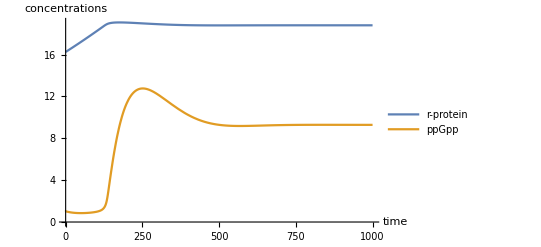

```mathematica
ClearAll[solt]
solt[PARS_]:=Module[{solTMP,minAAsyn,rcrit},
solTMP=NDSolve[
Join[sys,init]/.PARS,
vars,
{t,0,tmax},
Method->"StiffnessSwitching"
];
Flatten[{solTMP,PARS}]
]
(*Usage*)
sol = solt[pars];
Plot[Evaluate[{r[t],ppGpp[t]}/.sol],
{t,0,1000},
AxesLabel->{"time","concentrations"}
]
```

```mathematica
ClearAll[ss]
(*Use this function to calculate the steady state of the system. It first approximates this by evolving the system using solt, and than uses FindRoot to solve the system numerically.*)
ss[PARS_]:=Module[{tsolTEMP,aaguess,taaguess,ppGppguess,rguess,solTEMP,minAAsyn,rcrit},
tsolTEMP=solt[PARS];
aaguess=Flatten[{#,Max[#[tmax]/.tsolTEMP,10*$MachineEpsilon],$MachineEpsilon,∞}]&/@aaSpecies;
taaguess=Flatten[{#,
Max[10*$MachineEpsilon,Min[#[tmax]/.tsolTEMP,(τ1*r[tmax]-$MachineEpsilon)/.tsolTEMP/.PARS]],
$MachineEpsilon,
τ1*rmax/.tsolTEMP/.PARS}]&/@taaSpecies;
ppGppguess={Flatten[{ppGpp,(ppGpp[tmax]/.tsolTEMP),$MachineEpsilon,∞}]};
rguess={Flatten[{r,Min[r[tmax]/.tsolTEMP,.99*rmax/.PARS],$MachineEpsilon,rmax/.PARS}]};
solTEMP=FindRoot[
Thread[0==sys⟦All,2⟧]/.x_[t]->x/.PARS,
Join[aaguess,taaguess,ppGppguess,rguess]];
Flatten[{
solTEMP,
relations/.x_[t]->x/.solTEMP/.PARS,
jR->(vR/.relations/.x_[t]->x/.solTEMP/.PARS)
}]//N
]
ss[pars]//TableForm;
```

```mathematica
(*Compare to optimum (see above)*)
```

```mathematica
r/.opt
r/.ss[pars]
```

18.4814

18.7982

```mathematica
(drate/.ss[pars]/.pars)/(drate/.opt)(*Doubling rate, relative to optimum*)
```

0.997176

```mathematica
(*Lower and higher nutrient quality*)
parsLowNutrient =pars/.Thread[ Thread[(kn/.appendAllI)->_]->Thread[(kn/.appendAllI)->.5*(kn/.appendAllI/.pars)] ];
parsHighNutrient =pars/. Thread[Thread[(kn/.appendAllI)->_]->Thread[(kn/.appendAllI)->2*(kn/.appendAllI/.pars)] ];
```

```mathematica
steadystates = {
{drate,r/rmax}/.ss[parsLowNutrient]/.parsLowNutrient,
{drate,r/rmax}/.ss[pars]/.pars,
{drate,r/rmax}/.ss[parsHighNutrient]/.parsHighNutrient}
```

{{1.0032,0.165689},{1.70586,0.231356},{2.61143,0.334248}}

```mathematica
optima = {
{drate,r/rmax}/.optimum[parsLowNutrient]/.parsLowNutrient,
{drate,r/rmax}/.optimum[pars]/.pars,
{drate,r/rmax}/.optimum[parsHighNutrient]/.parsHighNutrient}
```

{{1.02492,0.144214},{1.7107,0.227457},{2.61942,0.336807}}

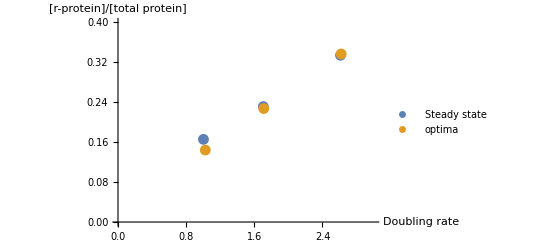

```mathematica
ListPlot[{steadystates,optima},
PlotRange->{{0,3},{0,0.4}},
AxesLabel->{"Doubling rate","[r-protein]/[total protein]"}
]
```

```mathematica
(*The calculatations below show that κrt and vSpoTSynt can be changed by an order of magnutide in either direction without affecting the model outcome.*)
```

```mathematica
ssLowkrt=ss[pars/.Rule[κrt->_,κrt->50]];
optLowkrt=optimum[pars/.Rule[κrt->_,κrt->50]];
(drate/.ssLowkrt/.pars)/(drate/.optLowkrt)
```

0.973291

```mathematica
ssHighkrt=ss[pars/.Rule[κrt->_,κrt->5000]];
optHighkrt=optimum[pars/.Rule[κrt->_,κrt->5000]];
(drate/.ssHighkrt/.pars)/(drate/.optHighkrt)
```

0.952831

```mathematica
ssHignvSpoT=ss[pars/.Rule[vSpoTSynt->_,vSpoTSynt->0.01]];
ssLowvSpoT=ss[pars/.Rule[vSpoTSynt->_,vSpoTSynt->0.0001]];
(drate/.ssHignvSpoT/.pars)/(drate/.opt)
(drate/.ssLowvSpoT/.pars)/(drate/.opt)
```

0.997414

0.997152